```mathematica
07 Jan 2020
Checked on 15 October 2020
```

12120 October

```mathematica
Solvind π^(..) = (π')^2 and finding the solutions.
```

```mathematica
(*Just to show the derivative in a traditional form*)
```

```mathematica
Clear["Global`*"];
```

```mathematica
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

```mathematica
Eq2[t_,x_]:= D[pi[t,x], t,t]  - D[pi[t,x], x] D[pi[t,x], x] ;
```

```mathematica
Eq2[t,x]==0//pdConv
```

(∂^2 pi(t,x))/(∂t^2)-((∂pi(t,x))/(∂x))^2==0

```mathematica
assum2[t_,x_] := a[t] x^2;
```

```mathematica
NewEq2=Block[{pi},pi[t_,x_]:=assum2[t,x];Eq2[t,x]]
```

-4 x^2 a[t]^2+x^2 a''[t]

```mathematica
For[i=1,i<6,i++,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq2,x^i]]]
```

x: 0

x^2: -4 a[t]^2+a''[t]

x^3: 0

x^4: 0

x^5: 0

```mathematica
Solvind the full equation π^(..) +Lin=NL
```

```mathematica
(*Definition of Ψ and the linear term*)
```

```mathematica
Ψ[τ_,x_]:=ψ0[τ] +ψ1[τ] x + ψ2[τ] x^2 +ψ3[τ] x^3+ ψ4[τ] x^4;
```

```mathematica
(*L[t_,x_] := 2/t(1-3w)∂_t pi[t,x] + (-2/t^2-3w 4/t^2+3 cs2 6/t^2)pi[t,x]+6/t(w-cs2)Ψ[x]-cs2∂_(x,x) pi[t,x];*)
L[τ_,x_] := Subscript[l, πd][τ]D[pi[τ,x], τ] + Subscript[l, π][τ]pi[τ,x]+Subscript[l, Ψ][τ] Ψ[τ,x]+Subscript[l, Ψd][τ] D[Ψ[τ,x], τ]+Subscript[l, πpp][τ]D[pi[τ,x], x,x];
```

```mathematica
Print[L[τ,r]//pdConv]
```

l_πpp(τ) (∂^2 pi(τ,r))/(∂r^2)+l_πd(τ) (∂pi(τ,r))/(∂τ)+l_π(τ) pi(τ,r)+l_Ψ(τ) (r^4 ψ4(τ)+r^3 ψ3(τ)+r^2 ψ2(τ)+r ψ1(τ)+ψ0(τ))+l_Ψd(τ) (r^4 (∂ψ4(τ))/(∂τ)+r^3 (∂ψ3(τ))/(∂τ)+r^2 (∂ψ2(τ))/(∂τ)+r (∂ψ1(τ))/(∂τ)+(∂ψ0(τ))/(∂τ))

```mathematica
(*Definition of non-linear term*)
```

```mathematica
NonLin[τ_,x_]:= Subscript[ν, πpp][τ] (D[pi[τ,x], x])^2 +Subscript[ν, πpπpd][τ]D[pi[τ,x], x]D[pi[τ,x], t,x] + Subscript[ν, ππpp][τ] pi[τ,x]D[pi[τ,x], x,x]+Subscript[ν, πdπpp][τ] D[pi[τ,x], t] D[pi[τ,x], x,x]+Subscript[ν, Ψπpp][τ] Ψ[τ,x] D[pi[τ,x], x,x]+Subscript[ν, Ψpπp][τ] D[Ψ[τ,x], x]D[pi[τ,x], x]+Subscript[ν, πpπpπpp][τ](D[pi[τ,x], x])^2 D[pi[τ,x], x,x];
```

```mathematica
(*Printing non-linear terms and checked *)
```

```mathematica
Print[NonLin[τ,x]//pdConv];
```

ν_ππpp(τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)+ν_πpπpπpp(τ) (∂^2 pi(τ,x))/(∂x^2) ((∂pi(τ,x))/(∂x))^2+ν_Ψpπp(τ) (∂pi(τ,x))/(∂x) (ψ1(τ)+4 x^3 ψ4(τ)+3 x^2 ψ3(τ)+2 x ψ2(τ))+ν_Ψπpp(τ) (∂^2 pi(τ,x))/(∂x^2) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))+ν_πpp(τ) ((∂pi(τ,x))/(∂x))^2

```mathematica
The full equation without linear terms
```

equation full linear terms The without

```mathematica
Eq[t_,x_]:= D[pi[t,x], t,t]+1*L[t,x]-NonLin[t,x];
```

```mathematica
Print[Eq[τ,x]//pdConv];
```

l_πpp(τ) (∂^2 pi(τ,x))/(∂x^2)+l_πd(τ) (∂pi(τ,x))/(∂τ)+l_π(τ) pi(τ,x)-ν_ππpp(τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)-ν_πpπpπpp(τ) (∂^2 pi(τ,x))/(∂x^2) ((∂pi(τ,x))/(∂x))^2-ν_Ψpπp(τ) (∂pi(τ,x))/(∂x) (ψ1(τ)+4 x^3 ψ4(τ)+3 x^2 ψ3(τ)+2 x ψ2(τ))-ν_Ψπpp(τ) (∂^2 pi(τ,x))/(∂x^2) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))-ν_πpp(τ) ((∂pi(τ,x))/(∂x))^2+(∂^2 pi(τ,x))/(∂τ^2)+l_Ψ(τ) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))+l_Ψd(τ) ((∂ψ0(τ))/(∂τ)+x^4 (∂ψ4(τ))/(∂τ)+x^3 (∂ψ3(τ))/(∂τ)+x^2 (∂ψ2(τ))/(∂τ)+x (∂ψ1(τ))/(∂τ))

```mathematica
assum[t_,x_] := Subscript[u, 0][t]+ Subscript[u, 1][t]x +  Subscript[u, 2][t] x^2+Subscript[u, 3][t] x^3+Subscript[u, 4][t] x^4;
```

```mathematica
NewEq=Block[{pi},pi[τ_,x_]:=Subscript[u, 0][τ]+ Subscript[u, 1][τ]x +  Subscript[u, 2][τ] x^2+Subscript[u, 3][τ] x^3+Subscript[u, 4][τ] x^4;Eq[τ,x]]
```

(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) l_Ψ[τ]+l_πpp[τ] (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ])+l_π[τ] (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπpπpp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ]) ν_ππpp[τ]-(ψ1[τ]+2 x ψ2[τ]+3 x^2 ψ3[τ]+4 x^3 ψ4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_Ψpπp[τ]-(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_Ψπpp[τ]+l_Ψd[τ] (ψ0'[τ]+x ψ1'[τ]+x^2 ψ2'[τ]+x^3 ψ3'[τ]+x^4 ψ4'[τ])+l_πd[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])+u_0''[τ]+x u_1''[τ]+x^2 u_2''[τ]+x^3 u_3''[τ]+x^4 u_4''[τ]

```mathematica
(*NewEq//Simplify*)
```

```mathematica
(*coefficient for x^0*)
```

```mathematica
(*NewEq /.{x->0}*)
```

```mathematica
(*NewEq /.{x->0}*)
```

```mathematica
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

x^0: (ψ0[τ] l_Ψ[τ]+l_π[τ] u_0[τ]+2 l_πpp[τ] u_2[τ]-u_1[τ]^2 ν_πpp[τ]-2 u_1[τ]^2 u_2[τ] ν_πpπpπpp[τ]-2 u_0[τ] u_2[τ] ν_ππpp[τ]-ψ1[τ] u_1[τ] ν_Ψpπp[τ]-2 ψ0[τ] u_2[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ0'[τ]+l_πd[τ] u_0'[τ]+u_0''[τ])

x: ψ1[τ] l_Ψ[τ]+l_π[τ] u_1[τ]+6 l_πpp[τ] u_3[τ]-4 u_1[τ] u_2[τ] ν_πpp[τ]-8 u_1[τ] u_2[τ]^2 ν_πpπpπpp[τ]-6 u_1[τ]^2 u_3[τ] ν_πpπpπpp[τ]-2 u_1[τ] u_2[τ] ν_ππpp[τ]-6 u_0[τ] u_3[τ] ν_ππpp[τ]-2 ψ2[τ] u_1[τ] ν_Ψpπp[τ]-2 ψ1[τ] u_2[τ] ν_Ψpπp[τ]-2 ψ1[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ0[τ] u_3[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ1'[τ]+l_πd[τ] u_1'[τ]+u_1''[τ]

x^2: ψ2[τ] l_Ψ[τ]+l_π[τ] u_2[τ]+12 l_πpp[τ] u_4[τ]-4 u_2[τ]^2 ν_πpp[τ]-6 u_1[τ] u_3[τ] ν_πpp[τ]-8 u_2[τ]^3 ν_πpπpπpp[τ]-36 u_1[τ] u_2[τ] u_3[τ] ν_πpπpπpp[τ]-12 u_1[τ]^2 u_4[τ] ν_πpπpπpp[τ]-2 u_2[τ]^2 ν_ππpp[τ]-6 u_1[τ] u_3[τ] ν_ππpp[τ]-12 u_0[τ] u_4[τ] ν_ππpp[τ]-3 ψ3[τ] u_1[τ] ν_Ψpπp[τ]-4 ψ2[τ] u_2[τ] ν_Ψpπp[τ]-3 ψ1[τ] u_3[τ] ν_Ψpπp[τ]-2 ψ2[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ1[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ0[τ] u_4[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ2'[τ]+l_πd[τ] u_2'[τ]+u_2''[τ]

x^3: ψ3[τ] l_Ψ[τ]+l_π[τ] u_3[τ]-12 u_2[τ] u_3[τ] ν_πpp[τ]-8 u_1[τ] u_4[τ] ν_πpp[τ]-48 u_2[τ]^2 u_3[τ] ν_πpπpπpp[τ]-36 u_1[τ] u_3[τ]^2 ν_πpπpπpp[τ]-64 u_1[τ] u_2[τ] u_4[τ] ν_πpπpπpp[τ]-8 u_2[τ] u_3[τ] ν_ππpp[τ]-12 u_1[τ] u_4[τ] ν_ππpp[τ]-4 ψ4[τ] u_1[τ] ν_Ψpπp[τ]-6 ψ3[τ] u_2[τ] ν_Ψpπp[τ]-6 ψ2[τ] u_3[τ] ν_Ψpπp[τ]-4 ψ1[τ] u_4[τ] ν_Ψpπp[τ]-2 ψ3[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ2[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ1[τ] u_4[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ3'[τ]+l_πd[τ] u_3'[τ]+u_3''[τ]

x^4: ψ4[τ] l_Ψ[τ]+l_π[τ] u_4[τ]-9 u_3[τ]^2 ν_πpp[τ]-16 u_2[τ] u_4[τ] ν_πpp[τ]-90 u_2[τ] u_3[τ]^2 ν_πpπpπpp[τ]-80 u_2[τ]^2 u_4[τ] ν_πpπpπpp[τ]-120 u_1[τ] u_3[τ] u_4[τ] ν_πpπpπpp[τ]-6 u_3[τ]^2 ν_ππpp[τ]-14 u_2[τ] u_4[τ] ν_ππpp[τ]-8 ψ4[τ] u_2[τ] ν_Ψpπp[τ]-9 ψ3[τ] u_3[τ] ν_Ψpπp[τ]-8 ψ2[τ] u_4[τ] ν_Ψpπp[τ]-2 ψ4[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ3[τ] u_3[τ] ν_Ψπpp[τ]-12 ψ2[τ] u_4[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ4'[τ]+l_πd[τ] u_4'[τ]+u_4''[τ]

```mathematica
-(-90 ζ a[t] b[t]^2-8 k η c[t]-12 k ν c[t]-80 ζ a[t]^2 c[t]-120 ζ b[t] c[t] d[t]-9 b[t]^2 α[t]-16 a[t] c[t] α[t]-6 b[t]^2 γ[t]-14 a[t] c[t] γ[t]+c[t] Δ[t]-8 β c[t] a'[t]-12 χ c[t] a'[t]-9 β b[t] b'[t]-6 χ b[t] b'[t]-8 β a[t] c'[t]-2 χ a[t] c'[t]+Γ[t] c'[t])
```

90 ζ a[t] b[t]^2+8 k η c[t]+12 k ν c[t]+80 ζ a[t]^2 c[t]+120 ζ b[t] c[t] d[t]+9 b[t]^2 α[t]+16 a[t] c[t] α[t]+6 b[t]^2 γ[t]+14 a[t] c[t] γ[t]-c[t] Δ[t]+8 β c[t] a'[t]+12 χ c[t] a'[t]+9 β b[t] b'[t]+6 χ b[t] b'[t]+8 β a[t] c'[t]+2 χ a[t] c'[t]-Γ[t] c'[t]

```mathematica
(*(*Factorizing a^2:*)
(*x2Eq=-4 η a[t]-2 ν a[t]-8 ζ a[t]^3-4 a[t]^2 α[t]-2 a[t]^2 γ[t]-4 β a[t] a'[t]-2 χ a[t] a'[t]+a''[t];*)
(*Collect[x2Eq,a[t]]*)
-8 ζ a[t]^3+a[t]^2 (-4 α[t]-2 γ[t])+a[t] (-4 η-2 ν-4 β a'[t]-2 χ a'[t])+a''[t]
(*x3Eq=-6 η b[t]-6 ν b[t]-48 ζ a[t]^2 b[t]-12 a[t] b[t] α[t]-8 a[t] b[t] γ[t]-6 β b[t] a'[t]-6 χ b[t] a'[t]-6 β a[t] b'[t]-2 χ a[t] b'[t]+b''[t];*)
(*Collect[x3Eq,a[t]]*)
-6 η b[t]-6 ν b[t]-48 ζ a[t]^2 b[t]-6 β b[t] a'[t]-6 χ b[t] a'[t]+a[t] (-12 b[t] α[t]-8 b[t] γ[t]-6 β b'[t]-2 χ b'[t])+b''[t]
(*x4Eq=-90 ζ a[t] b[t]^2-8 η c[t]-12 ν c[t]-80 ζ a[t]^2 c[t]-9 b[t]^2 α[t]-16 a[t] c[t] α[t]-6 b[t]^2 γ[t]-14 a[t] c[t] γ[t]-8 β c[t] a'[t]-12 χ c[t] a'[t]-9 β b[t] b'[t]-6 χ b[t] b'[t]-8 β a[t] c'[t]-2 χ a[t] c'[t]+c''[t];*)
(*Collect[x4Eq,a[t]]*)
-8 η c[t]-12 ν c[t]-80 ζ a[t]^2 c[t]-9 b[t]^2 α[t]-6 b[t]^2 γ[t]-8 β c[t] a'[t]-12 χ c[t] a'[t]-9 β b[t] b'[t]-6 χ b[t] b'[t]+a[t] (-90 ζ b[t]^2-16 c[t] α[t]-14 c[t] γ[t]-8 β c'[t]-2 χ c'[t])+c''[t]*)
```

```mathematica
Solving the coupled ODEs:
```

```mathematica
tini=0.01;tf=45;
w=-0.8;cs2=0.9;
α[t] = -1/t(5 cs2 +3w -2);
βval =2 (1-cs2); 
γ[t]=-2/t((cs2-1)+3cs2 (1+w));
χval = -(cs2-1);
νval=(cs2-1);
ηval=(cs2-1);
ζval=3/2(cs2-1);
k = 20;
Γ[t] = 2/t(1-3 w);
Δ[t] = -2/t^2-3w 4/t^2+3cs2 6/t^2;
Θ[t] = 6/t(w-cs2);
Λ=-cs2;
```

```mathematica
eqn0=NewEq/.{x->0,β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval};
eqn1=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^1];
eqn2=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^2];
eqn3=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^3];
eqn4=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^4];
```

```mathematica
s=NDSolve[{eqn3==0,eqn1==0,eqn2==0,eqn4==0,eqn0==0,a[tini]==0.0,a'[tini]==0.0,b[tini]==0.,b'[tini]==-0.0,c[tini]==0.,c'[tini]==0.0,d[tini]==0.,d'[tini]==0.0,e[tini]==0.,e'[tini]==0.0},{a[t],a'[t],b[t],b'[t],c[t],c'[t],d[t],d'[t],e[t],e'[t]},{t,tini,tf}]
```

{{a[t]→InterpolatingFunction[…][t],a'[t]→InterpolatingFunction[…][t],b[t]→InterpolatingFunction[…][t],b'[t]→InterpolatingFunction[…][t],c[t]→InterpolatingFunction[…][t],c'[t]→InterpolatingFunction[…][t],d[t]→InterpolatingFunction[…][t],d'[t]→InterpolatingFunction[…][t],e[t]→InterpolatingFunction[…][t],e'[t]→InterpolatingFunction[…][t]}}

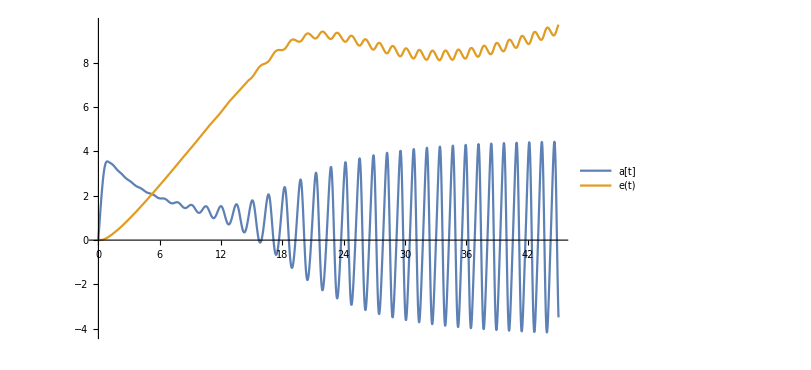

```mathematica
plt = Plot[Evaluate[{a[t],e[t]}/.s],{t,tini,tf},PlotRange->Full,PlotLegends->{"a[t]","e(t)"}, PlotStyle->Thick, ImageSize->600]
```